# Q: Generate Gr(4,7) with A-mutations

```mathematica
SetDirectory[NotebookDirectory[]];
<<tools.m;
```

```mathematica
Tally[Length[Complement[Variables[(g47ify/@#[[1]])],goodBrs[7]]]&/@e6[]]
```

{{2,252},{1,266},{3,56},{0,259}}

```mathematica
a[1]=br[1,3,4,5];
a[2]=br[1,2,4,5];
a[3]=br[1,2,3,5];
a[4]=br[3,4,5,7];
a[5]=br[1,4,5,7];
a[6]=br[1,2,5,7];
a[7]=br[2,3,4,5];
a[8]=br[1,2,3,4];
a[9]=br[1,2,3,7];
a[10]=br[1,2,6,7];
a[11]=br[1,5,6,7];
a[12]=br[4,5,6,7];
a[13]=br[3,4,5,6];
```

```mathematica
B={{0,-1,0,-1,1,0,1,0,0,0,0,0,0},{1,0,-1,0,-1,1,0,0,0,0,0,0,0},
{0,1,0,0,0,-1,0,-1,1,0,0,0,0},
{1,0,0,0,-1,0,0,0,0,0,0,1,-1},
{-1,1,0,1,0,-1,0,0,0,0,1,-1,0},
{0,-1,1,0,1,0,0,0,-1,1,-1,0,0}};
```

```mathematica
g47SeedFull={a/@Range[13],B};
```

```mathematica
seed=g47SeedFull//num[7];
```

```mathematica
fullSchouten[target_]:=Module[{},
If[MemberQ[{br,ccap1},Head[target]],Return[target]];
tmpAns=Factor[target]//.schoutens[7];
If[Head[tmpAns]===Times,Return[tmpAns]];
opts=goodLetters[7][[#]]&/@Flatten[Position[IntegerQ/@(num[7][target]/num[7][goodLetters[7]]),True]];
tmp=Abs[numRand[7][{opts,target}]];
tmpAns=Times@@(opts^(p/@Range[Length[opts]]))//.solve[(List@@((Times@@(tmp[[1]]^(p/@Range[Length[opts]])))/tmp[[2]]))/.a_^b_:>b];
factor=Which[num[7][target/tmpAns]==-1,-1,num[7][target/tmpAns]==1,1,Abs[num[7][target/tmpAns]]≠1,Abort[]];
tmpAns=factor*tmpAns;
If[Complement[Variables[tmpAns],goodLetters[7]]=={},Return[tmpAns],Abort[]];]
```

```mathematica
mutateASchouten[k_][cluster_]:=With[{hold=mutateA[k][cluster]//.schoutens[7]},{fullSchouten/@hold[[1]],hold[[2]]}];
```

```mathematica
mutationASchouten[i___][cluster_]:=ComposeList[mutateASchouten/@{i},cluster][[-1]];
```

```mathematica
rank=6;
doMutation[x___]:=doMutation[x]=Sort[(mutationA[x][seed])[[1]]];
mutationList=Prepend[{#}&/@Range[rank],{}];
```

```mathematica
mutationList
```

{{},{1},{2},{3},{4},{5},{6}}

```mathematica
knownClusters=Union[Sort/@doMutation@@@mutationList];
```

```mathematica
Do[boundary=Select[mutationList,Length[#]==depth-1&];
Print[{depth,Length[knownClusters]}];
newMutations=DeleteCases[Flatten[Table[Append[boundary[[i]],#]&/@Range[rank],{i,Length[boundary]}],1],{a___,b_,b_}];
newMutationsGood=Select[newMutations,!MemberQ[knownClusters,doMutation@@#]&];
duplicates=Gather[newMutationsGood,(doMutation@@#1)==(doMutation@@#2)&];
newMutationsGoodReduce=#[[1]]&/@duplicates;
If[Length[newMutationsGood]==0,Break[]];
mutationList=Join[mutationList,newMutationsGoodReduce];
knownClusters=Union[doMutation@@@mutationList],{depth,2,12}];
```

{2,7}

{3,31}

{4,93}

{5,215}

{6,397}

{7,605}

{8,769}

{9,825}

{10,833}

```mathematica
g47=Monitor[Table[Append[(mutationASchouten@@mutationList[[aaa]])[g47SeedFull],mutationList[[aaa]]],{aaa,Length[mutationList]}],aaa];
```

```mathematica
graph[cluster_]:=Graph[Join[Union[Flatten[Table[f[i,j]cluster[[2,i,j]],{i,6},{j,13}]/.-f[a_,b_]:>f[b,a]]][[2;;-1]],Table[f[i,14],{i,7,13}],{f[8,7],f[7,13],f[13,12],f[12,11],f[11,10],f[10,9],f[9,8]}]/.f:>DirectedEdge,VertexLabels->"Name"];
```

```mathematica
graphNew[cluster_]:=Block[{names=Join[(cluster[[1,1;;6]]/.{br[x__]:>Row[{"(",x,")"}]}),(cluster[[1,7;;-1]]/.{br[x__]:>Row[Style[#,Red]&/@{"(",x,")"}]})]},Graph[Union[Flatten[Table[f[i,j]cluster[[2,i,j]],{i,6},{j,13}]/.-f[a_,b_]:>f[b,a]]][[2;;-1]]/.f:>DirectedEdge,VertexLabels->Thread[Rule[Range[13],names]]]];
```

```mathematica
goods=Select[g47,PlanarGraphQ[graph[#]]&];
```

mutating a node of valence 6 gives you non-planar, mutating at node of valence 4 gives you planar.

```mathematica
Union[Table[(PlanarGraphQ[graph[mutationASchouten[#][goods[[aa]]]]]&/@Range[6])==((Total/@Abs[goods[[aa,2]]])/.{4->True,6->False}),{aa,Length[goods]}]]
```

{True}

```mathematica
Tally[Total/@Abs[Flatten[#[[2]]&/@g47,1]]]
```

{{4,1876},{6,532},{3,1498},{5,952},{7,140}}

```mathematica
Tally[Total/@Abs[Flatten[#[[2]]&/@goods,1]]]
```

{{4,1288},{6,266}}

given my current planarQ, it also appears that having nodes of valence other than 4 or 6 is equivalent to non-planar. this should have a strong impact on the types of subalgebras we can get!

```mathematica
xCoords[cluster_]:=
FullSimplify[Table[Product[cluster[[1,j]]^cluster[[2,i,j]],{j,Length[cluster[[1]]]}],{i,Length[cluster[[2]]]}]]
```

```mathematica
g47Xs=Table[{xCoords[g47[[aa]]],-#[[1;;6]]&/@g47[[aa,2]],g47[[aa,3]]},{aa,Length[g47]}];
```

```mathematica
isGood[a_]:=isGoodEval[sortInverse[num[7][g47ify/@a]]];
```

```mathematica
Table[isGoodEval[sortInverse[num[7][g47Xs[[aaa,1]]]]]=PlanarGraphQ[graph[g47[[aaa]]]],{aaa,Length[g47]}];
```

```mathematica
Count[isGood/@(#[[1]]&/@e6[]),True]
```

259

```mathematica
alg=e6[];
```

```mathematica
subalgs=subalg[alg][a3];
```

```mathematica
Length[subalgs]
```

364

```mathematica
countA3s=Monitor[Table[Count[isGood/@(#[[1]]&/@(cluster[alg]/@subalgCoords[alg][subalgs[[aaa]]])),False],{aaa,Length[subalgs]}],aaa];
```

```mathematica
subalgCoords[alg][subalgs[[-1]]]
```

{{5,3,6,4,2,1,3},{5,6,3,4,2,1,6},{5,3,2,6,4,1,3},{5,3,6,4,2,1,3,5},{5,6,3,2,4,1,6,2},{5,6,3,4,2,1,6,5},{2,5,3,6,2,4,1,6},{5,3,2,6,4,1,3,5},{5,3,2,6,4,1,3,5,2},{5,6,3,2,4,1,6,2,5},{5,6,3,4,2,1,6,5,4},{2,3,5,6,2,4,1,3,6},{2,3,5,6,2,4,1,6,3},{1,3,2,5,6,4,3,1,5,2}}

```mathematica
nodeCount[cluster_]:=Total/@Abs[cluster[[2]]];
```

```mathematica
nodeCount[e6Seed]
```

{1,2,3,1,2,1}

```mathematica
g47SeedFull[[1]]
```

{br[1,3,4,5],br[1,2,4,5],br[1,2,3,5],br[3,4,5,7],br[1,4,5,7],br[1,2,5,7],br[2,3,4,5],br[1,2,3,4],br[1,2,3,7],br[1,2,6,7],br[1,5,6,7],br[4,5,6,7],br[3,4,5,6]}

```mathematica
Sort[Table[{xCoords[g47SeedFull][[i]],nodeCount[g47SeedFull][[i]]},{i,6}]]
```

{{(br[1,2,3,7] br[1,2,4,5])/(br[1,2,3,4] br[1,2,5,7]),4},{(br[1,2,5,7] br[1,3,4,5])/(br[1,2,3,5] br[1,4,5,7]),4},{(br[1,2,3,5] br[1,2,6,7] br[1,4,5,7])/(br[1,2,3,7] br[1,2,4,5] br[1,5,6,7]),6},{(br[1,4,5,7] br[2,3,4,5])/(br[1,2,4,5] br[3,4,5,7]),4},{(br[1,2,4,5] br[1,5,6,7] br[3,4,5,7])/(br[1,2,5,7] br[1,3,4,5] br[4,5,6,7]),6},{(br[1,3,4,5] br[4,5,6,7])/(br[1,4,5,7] br[3,4,5,6]),4}}

```mathematica
Sort[Table[{(g47ify/@e6[][[116,1]])[[i]],nodeCount[e6[][[116]]][[i]]},{i,6}]]
```

{{(br[1,2,3,7] br[1,2,4,5])/(br[1,2,3,4] br[1,2,5,7]),2},{(br[1,2,5,7] br[1,3,4,5])/(br[1,2,3,5] br[1,4,5,7]),4},{(br[1,2,3,5] br[1,2,6,7] br[1,4,5,7])/(br[1,2,3,7] br[1,2,4,5] br[1,5,6,7]),3},{(br[1,4,5,7] br[2,3,4,5])/(br[1,2,4,5] br[3,4,5,7]),3},{(br[1,2,4,5] br[1,5,6,7] br[3,4,5,7])/(br[1,2,5,7] br[1,3,4,5] br[4,5,6,7]),4},{(br[1,3,4,5] br[4,5,6,7])/(br[1,4,5,7] br[3,4,5,6]),2}}

```mathematica
Total/@Abs[g47[[1,2]]]
```

{4,4,4,4,6,6}

```mathematica
xCoords[g47[[1]]]
```

{(br[1,4,5,7] br[2,3,4,5])/(br[1,2,4,5] br[3,4,5,7]),(br[1,2,5,7] br[1,3,4,5])/(br[1,2,3,5] br[1,4,5,7]),(br[1,2,3,7] br[1,2,4,5])/(br[1,2,3,4] br[1,2,5,7]),(br[1,3,4,5] br[4,5,6,7])/(br[1,4,5,7] br[3,4,5,6]),(br[1,2,4,5] br[1,5,6,7] br[3,4,5,7])/(br[1,2,5,7] br[1,3,4,5] br[4,5,6,7]),(br[1,2,3,5] br[1,2,6,7] br[1,4,5,7])/(br[1,2,3,7] br[1,2,4,5] br[1,5,6,7])}

```mathematica
Sort[{#[[1]],Length[Intersection[Variables[#[[1]]],frozen]]+#[[2]]}&/@Out[679]]==Sort[Table[{xCoords[g47SeedFull][[i]],nodeCount[g47SeedFull][[i]]},{i,6}]]
```

True

```mathematica
frozen=Sort[(List@@addCyclic[7][br[1,2,3,4]])/.-a_:>a];
```

```mathematica
nodeCount[e6[][[116]]]
```

{2,2,3,4,4,3}

```mathematica
g47ify/@e6[][[116,1]]
```

{(br[1,2,3,7] br[1,2,4,5])/(br[1,2,3,4] br[1,2,5,7]),(br[1,3,4,5] br[4,5,6,7])/(br[1,4,5,7] br[3,4,5,6]),(br[1,2,3,5] br[1,2,6,7] br[1,4,5,7])/(br[1,2,3,7] br[1,2,4,5] br[1,5,6,7]),(br[1,2,5,7] br[1,3,4,5])/(br[1,2,3,5] br[1,4,5,7]),(br[1,2,4,5] br[1,5,6,7] br[3,4,5,7])/(br[1,2,5,7] br[1,3,4,5] br[4,5,6,7]),(br[1,4,5,7] br[2,3,4,5])/(br[1,2,4,5] br[3,4,5,7])}

```mathematica
ratios[7]
```

{(br[1,2,3,4] br[1,2,5,6])/(br[1,2,3,6] br[1,2,4,5]),383,-(br[3,4,5,6] ccap1[7,tup[1,6],1,tup[4,5]])/(br[1,3,6,7] br[2,3,4,5] br[4,5,6,7])}
 |  |  |  |

```mathematica
e6Num=Table[sortInverse[num[7][g47ify/@e6[][[aaa,1]]]],{aaa,Length[e6[]]}];
```

```mathematica
Position[countA3s,0]
```

{{21},{77},{83},{93},{122},{204},{321}}

```mathematica
Sort[Tally[countA3s]]
```

{{0,7},{4,84},{7,84},{9,56},{10,28},{11,56},{14,49}}

```mathematica
subalgs=subalg[alg][a2];
```

```mathematica
Length[subalgs]
```

504

```mathematica
countA2s=Monitor[Table[Count[isGood/@(#[[1]]&/@(cluster[alg]/@subalgCoords[alg][subalgs[[aaa]]])),False],{aaa,Length[subalgs]}],aaa];
```

```mathematica
Sort[Tally[countA2s]]
```

{{0,60},{2,168},{3,84},{4,56},{5,136}}

```mathematica
preMutate[a_]:=If[a=={},{},a[[1;;-2]]];
```

```mathematica
Max[Length[If[#=={},0,Variables[g47ify[(mutation@@preMutate[#])[e6Seed][[1,#[[-1]]]]]]]]&@#&/@subalgCoords[alg][subalgs[[1]]]]
```

5

```mathematica
countA3s2=Max[Length[Variables[#]]&/@(g47ify/@sortInverse[Flatten[#[[1]]&/@fullSub[alg][subalgs[[#]]]]])]&/@Range[Length[subalgs]];
```

```mathematica
Sort[Tally[countA3s2]]
```

{{4,7},{5,14},{6,168},{7,175}}

```mathematica
tbl=Table[Sort[goods[[aa,1,1;;6]]],{aa,Length[goods]}];
```

```mathematica
myList=Union[Table[Sort/@((List@@(addCyclic[7][f[tbl[[pp]]]]/.-a_:>a))/.f[a_]:>a),{pp,Length[tbl]}]];
```

```mathematica
Length[myList]
```

37

```mathematica
myList=Union[Table[Sort[Sort/@((List@@(addCyclic[7][f[tbl[[pp]]]]/.-a_:>a))/.f[a_]:>a)],{pp,Length[tbl]}]];
```

```mathematica
jakeList={{{1,2,4,7},{1,3,4,7},{1,4,6,7},{2,3,4,6},{2,3,4,7},{3,4,6,7}},{{1,3,4,7},{1,3,6,7},{1,4,6,7},{2,3,4,6},{2,3,4,7},{3,4,6,7}},{{1,2,4,7},{1,4,6,7},{2,3,4,6},{2,3,4,7},{2,4,6,7},{3,4,6,7}},{{1,4,6,7},{2,3,4,6},{2,3,4,7},{2,3,6,7},{2,4,6,7},{3,4,6,7}},{{1,3,6,7},{1,4,6,7},{2,3,4,6},{2,3,4,7},{2,3,6,7},{3,4,6,7}},{{1,2,4,7},{2,3,4,6},{2,3,4,7},{2,4,6,7},{2,5,6,7},{3,4,6,7}},{{2,3,4,6},{2,3,4,7},{2,3,6,7},{2,4,6,7},{2,5,6,7},{3,4,6,7}},{{1,3,4,7},{1,3,6,7},{2,3,4,6},{2,3,4,7},{3,4,6,7},{3,5,6,7}},{{1,3,6,7},{2,3,4,6},{2,3,4,7},{2,3,6,7},{3,4,6,7},{3,5,6,7}},{{1,2,4,7},{1,3,4,6},{1,3,4,7},{1,4,6,7},{2,3,4,6},{3,4,6,7}},{{1,2,4,6},{1,2,4,7},{1,3,4,6},{1,4,6,7},{2,3,4,6},{3,4,6,7}},{{1,2,3,6},{1,2,4,6},{1,3,4,6},{1,4,6,7},{2,3,4,6},{3,4,6,7}},{{1,2,3,6},{1,3,4,6},{1,3,6,7},{1,4,6,7},{2,3,4,6},{3,4,6,7}},{{1,2,4,6},{1,2,4,7},{1,4,6,7},{2,3,4,6},{2,4,6,7},{3,4,6,7}},{{1,2,3,6},{1,2,4,6},{1,4,6,7},{2,3,4,6},{2,4,6,7},{3,4,6,7}},{{1,2,3,6},{1,4,6,7},{2,3,4,6},{2,3,6,7},{2,4,6,7},{3,4,6,7}},{{1,2,3,6},{1,3,6,7},{1,4,6,7},{2,3,4,6},{2,3,6,7},{3,4,6,7}},{{1,2,4,6},{1,2,4,7},{2,3,4,6},{2,4,6,7},{2,5,6,7},{3,4,6,7}},{{1,2,3,6},{1,2,4,6},{2,3,4,6},{2,4,6,7},{2,5,6,7},{3,4,6,7}},{{1,2,3,6},{2,3,4,6},{2,3,6,7},{2,4,6,7},{2,5,6,7},{3,4,6,7}},{{1,2,3,6},{1,3,4,6},{1,3,6,7},{2,3,4,6},{3,4,6,7},{3,5,6,7}},{{1,2,3,6},{1,3,6,7},{2,3,4,6},{2,3,6,7},{3,4,6,7},{3,5,6,7}},{{1,2,4,7},{1,3,4,6},{1,3,4,7},{1,4,5,6},{1,4,6,7},{2,3,4,6}},{{1,2,4,6},{1,2,4,7},{1,3,4,6},{1,4,5,6},{1,4,6,7},{2,3,4,6}},{{1,2,3,6},{1,2,4,6},{1,3,4,6},{1,4,5,6},{1,4,6,7},{2,3,4,6}},{{1,2,3,6},{1,3,4,6},{1,3,6,7},{1,4,5,6},{1,4,6,7},{2,3,4,6}},{{1,2,3,6},{1,2,4,6},{2,3,4,6},{2,4,5,6},{2,4,6,7},{2,5,6,7}},{{1,2,3,6},{1,2,4,6},{1,2,5,6},{2,3,4,6},{2,4,5,6},{2,5,6,7}},{{1,2,3,6},{1,2,5,6},{2,3,4,6},{2,3,5,6},{2,4,5,6},{2,5,6,7}},{{1,3,6,7},{2,3,4,6},{2,3,4,7},{2,3,5,6},{2,3,6,7},{3,5,6,7}},{{1,2,4,7},{1,4,6,7},{2,3,4,6},{2,3,4,7},{2,4,5,6},{2,4,6,7}},{{1,4,6,7},{2,3,4,7},{2,3,6,7},{2,4,6,7},{3,4,5,7},{3,4,6,7}},{{1,2,3,6},{1,2,4,6},{1,3,4,5},{1,3,4,6},{1,4,5,6},{1,4,6,7}}};
```

```mathematica
br@@@jakeList[[1]]
```

{br[1,2,4,7],br[1,3,4,7],br[1,4,6,7],br[2,3,4,6],br[2,3,4,7],br[3,4,6,7]}

```mathematica
Position[Length[Intersection[#[[1]],{br[1,2,3,5],br[1,2,3,6],br[1,2,5,6],br[1,3,4,5],br[1,3,5,6],br[3,5,6,7]}]]&/@g47,6]
```

{{301}}

```mathematica
Position[jakeListBr,Sort[mutateASchouten[1][g47[[301]]][[1,1;;6]]]]
```

{{4,1}}

```mathematica
{br[1,3,4,5],br[1,2,5,6],br[1,2,3,5],br[1,3,5,6],br[3,5,6,7],br[1,2,3,6],br[2,3,4,5],br[1,2,3,4],br[1,2,3,7],br[1,2,6,7],br[1,5,6,7],br[4,5,6,7],br[3,4,5,6]}/.{br[x__]:>Row[{"(",x,")"}]}
```

{(1345),(1256),(1235),(1356),(3567),(1236),(2345),(1234),(1237),(1267),(1567),(4567),(3456)}

```mathematica
Function[{graphData},Block[{adj=(Sign[(#-Transpose[#])&@ArrayPad[graphData[[2]],{{0,7},{0,0}}]]/.{-1->0}),names=Join[(graphData[[1,1;;6]]/.{br[x__]:>Row[{"(",x,")"}]}),(graphData[[1,7;;-1]]/.{br[x__]:>Row[Style[#,Red]&/@{"(",x,")"}]})]},AdjacencyGraph[adj,VertexLabels->Thread[Rule[Range[13],names]]]]]@Out[785]
```

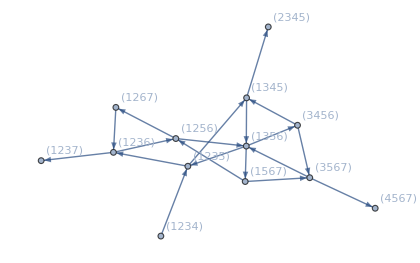

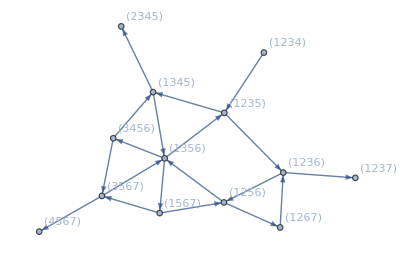

```mathematica
graphNew[g47[[301]]]
```

```mathematica
br@@@Sort/@Partition[Range[7],4,1,1];
Flatten[Position[Out[785][[1]],#]&/@%]
Complement[Range[7+6],%]
```

{8,7,13,12,11,10,9}

{1,2,3,4,5,6}

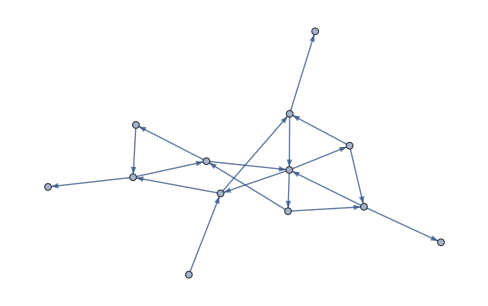

```mathematica
Function[{adj},(Sign[(#-Transpose[#])&@ArrayPad[adj,{{0,7},{0,0}}]]/.{-1->0})][Out[823]];
AdjacencyGraph[%,VertexLabel]
```

(0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 0
1 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{13,13}

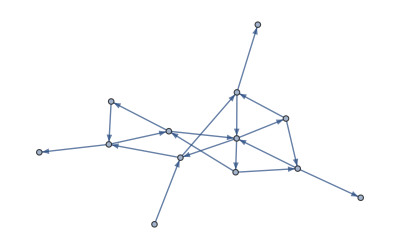

```mathematica
{{0,0,-1,1,0,0,1,0,0,0,0,0,-1},{0,0,0,1,0,-1,0,0,0,1,-1,0,0},{1,0,0,-1,0,1,0,-1,0,0,0,0,0},{-1,-1,1,0,-1,0,0,0,0,0,1,0,1},{0,0,0,1,0,0,0,0,0,0,-1,1,-1},{0,1,-1,0,0,0,0,0,1,-1,0,0,0}};
Sign[(#-Transpose[#])]&@ArrayPad[%,{{0,7},{0,0}}];
MatrixForm[%]
Dimensions[%]
AdjacencyGraph[(%%%/.{-1->0})]
```

```mathematica
{{0,0,-1,1,0,0,1,0,0,0,0,0,-1},{0,0,0,1,0,-1,0,0,0,1,-1,0,0},{1,0,0,-1,0,1,0,-1,0,0,0,0,0},{-1,-1,1,0,-1,0,0,0,0,0,1,0,1},{0,0,0,1,0,0,0,0,0,0,-1,1,-1},{0,1,-1,0,0,0,0,0,1,-1,0,0,0}}[[All,7;;-1]]
```

{{1,0,0,0,0,0,-1},{0,0,0,1,-1,0,0},{0,-1,0,0,0,0,0},{0,0,0,0,1,0,1},{0,0,0,0,-1,1,-1},{0,0,1,-1,0,0,0}}

```mathematica
{{0,0,-1,1,0,0,1,0,0,0,0,0,-1},{0,0,0,1,0,-1,0,0,0,1,-1,0,0},{1,0,0,-1,0,1,0,-1,0,0,0,0,0},{-1,-1,1,0,-1,0,0,0,0,0,1,0,1},{0,0,0,1,0,0,0,0,0,0,-1,1,-1},{0,1,-1,0,0,0,0,0,1,-1,0,0,0}}[[All,1;;6]];
MatrixForm[%]
```

(0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1
1 | 0 | 0 | -1 | 0 | 1
-1 | -1 | 1 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0)

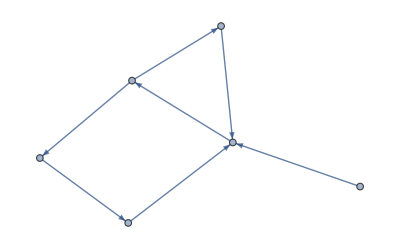

```mathematica
AdjacencyGraph[({{0,0,-1,1,0,0,1,0,0,0,0,0,-1},{0,0,0,1,0,-1,0,0,0,1,-1,0,0},{1,0,0,-1,0,1,0,-1,0,0,0,0,0},{-1,-1,1,0,-1,0,0,0,0,0,1,0,1},{0,0,0,1,0,0,0,0,0,0,-1,1,-1},{0,1,-1,0,0,0,0,0,1,-1,0,0,0}}[[All,1;;6]])/.{-1->0}]
```

```mathematica
jakeListBr=Table[Sort[Sort/@((List@@addCyclic[7][f[br@@@jakeList[[aa]]]]/.-a_:>a)/.f[a_]:>a)],{aa,Length[jakeList]}];
```

```mathematica
Flatten[Table[Position[Length[Intersection[#[[1]],Complement[myList,jakeListBr][[i,1]]]]&/@g47,6],{i,Length[Complement[myList,jakeListBr]]}]]
```

{301,146,33,640}

```mathematica
v
```

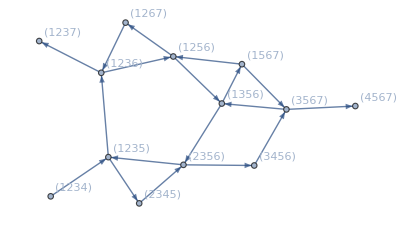

```mathematica
mutateASchouten[1][g47[[301]]]//graphNew
```

```mathematica
jakeListBr[[1]]
```

{{br[1,2,3,5],br[1,2,3,6],br[1,3,6,7],br[2,3,5,6],br[2,3,6,7],br[3,5,6,7]},{br[1,2,3,5],br[1,2,4,5],br[1,2,5,7],br[1,3,4,5],br[1,4,5,7],br[3,4,5,7]},{br[1,2,3,6],br[1,2,5,6],br[1,4,5,6],br[2,3,4,6],br[2,3,5,6],br[2,4,5,6]},{br[1,2,4,5],br[1,2,4,7],br[1,2,5,6],br[1,2,5,7],br[2,4,5,6],br[2,5,6,7]},{br[1,2,4,7],br[1,3,4,7],br[1,4,6,7],br[2,3,4,6],br[2,3,4,7],br[3,4,6,7]},{br[1,3,4,5],br[1,3,4,7],br[1,3,6,7],br[1,4,5,6],br[1,4,5,7],br[1,4,6,7]},{br[2,3,4,7],br[2,3,6,7],br[2,5,6,7],br[3,4,5,7],br[3,4,6,7],br[3,5,6,7]}}

```mathematica
Sort[Complement[mutateASchouten[1][g47[[146]]][[1]],br@@@Sort/@Partition[Range[7],4,1,1]]]
Position[jakeListBr,%]
```

{br[1,2,3,5],br[1,2,5,6],br[1,2,5,7],br[1,3,5,6],br[2,3,5,6],br[3,5,6,7]}

{{16,1}}

```mathematica
Sort[Complement[mutateASchouten[2][g47[[640]]][[1]],br@@@Sort/@Partition[Range[7],4,1,1]]]
Position[jakeListBr,%]
```

{br[1,2,3,6],br[1,2,4,6],br[1,4,6,7],br[2,3,4,6],br[2,4,5,6],br[2,4,6,7]}

{{33,3}}

```mathematica
jakeListBr[[4]]
```

{{br[1,2,3,5],br[1,2,3,6],br[1,2,5,6],br[1,3,5,6],br[2,3,5,6],br[3,5,6,7]},{br[1,2,3,6],br[1,2,4,5],br[1,2,4,6],br[1,2,5,6],br[1,4,5,6],br[2,4,5,6]},{br[1,2,4,5],br[1,2,4,7],br[1,2,5,7],br[1,4,5,7],br[2,4,5,6],br[2,4,5,7]},{br[1,2,5,7],br[1,3,4,5],br[1,3,4,7],br[1,3,5,7],br[1,4,5,7],br[3,4,5,7]},{br[1,3,4,5],br[1,3,4,6],br[1,3,4,7],br[1,3,6,7],br[1,4,6,7],br[3,4,6,7]},{br[1,4,6,7],br[2,3,4,6],br[2,3,4,7],br[2,3,6,7],br[2,4,6,7],br[3,4,6,7]},{br[2,3,4,7],br[2,3,5,6],br[2,3,5,7],br[2,3,6,7],br[2,5,6,7],br[3,5,6,7]}}

```mathematica
jakeList[[4]]
```

{{1,4,6,7},{2,3,4,6},{2,3,4,7},{2,3,6,7},{2,4,6,7},{3,4,6,7}}

```mathematica
{{301,1},{146,1},{33,2},{640,2}}
```

```mathematica
sys
```

```mathematica
mutateASchouten[2][g47[[640]]][[1,1]]
```

br[1,2,4,6]

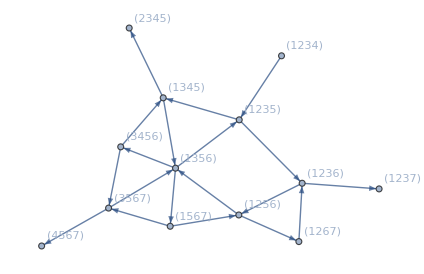
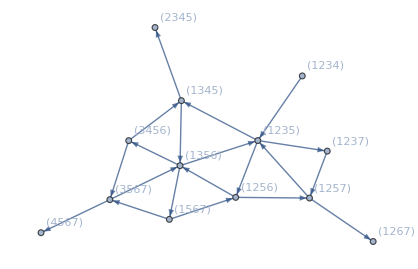
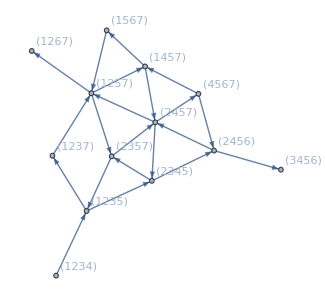
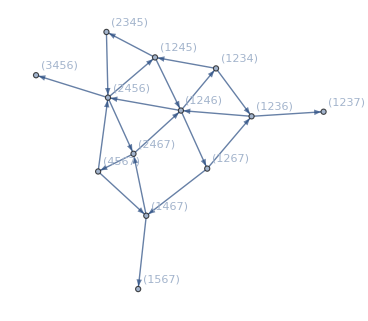

```mathematica
graphNew[g47[[#]]]&/@Out[909]
```

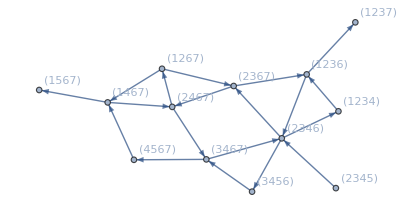

```mathematica
graphNew[goods[[-1]]]
```